Load some packaged we’ll use for plotting:

```mathematica
Needs["ErrorBarPlots`"]
Needs["PlotLegends`"]
```

Define the β parameter that shows up in the theoretical prediction for the diffraction pattern:

```mathematica
β:=0.5*(2π)/(632.8*10^-9)*0.08*10^-3 Sin[θ]
```

Define a table with our data and associated uncertainties:

```mathematica
data:={{{0.000,1.000},ErrorBar[0.001,0.025]},{{0.002,0.5795},ErrorBar[0.001,0.025]},{{0.004,0.3466},ErrorBar[0.001,0.025]},{{0.006,0.1648},ErrorBar[0.001,0.025]},{{0.008,0.0739},ErrorBar[0.001,0.025]},{{0.01,0.0568},ErrorBar[0.001,0.025]},{{0.012,0.0909},ErrorBar[0.001,0.025]},{{0.014,0.0568},ErrorBar[0.001,0.025]},{{0.016,0.0455},ErrorBar[0.001,0.025]},{{0.018,0.0398},ErrorBar[0.001,0.025]},{{0.02,0.0511},ErrorBar[0.001,0.025]},{{0.022,0.0568},ErrorBar[0.001,0.025]},{{0.024,0.0682},ErrorBar[0.001,0.025]},{{-0.002,0.5795},ErrorBar[0.001,0.025]},{{-0.004,0.3466},ErrorBar[0.001,0.025]},{{-0.006,0.1648},ErrorBar[0.001,0.025]},{{-0.008,0.0739},ErrorBar[0.001,0.025]},{{-0.01,0.0568},ErrorBar[0.001,0.025]},{{-0.012,0.0909},ErrorBar[0.001,0.025]},{{-0.014,0.0568},ErrorBar[0.001,0.025]},{{-0.016,0.0455},ErrorBar[0.001,0.025]},{{-0.018,0.0398},ErrorBar[0.001,0.025]},{{-0.02,0.0511},ErrorBar[0.001,0.025]},{{-0.022,0.0568},ErrorBar[0.001,0.025]},{{-0.024,0.0682},ErrorBar[0.001,0.025]}}
```

Draw the theoretical curve on a plot:

```mathematica
theory:=Plot[(Sin[ β]/β)^2,{θ,-1,1},Axes->True,PlotRangePadding->{0.01,0.05},PlotRange->{{-0.02,0.02},{0,1}},PlotStyle->Black,FrameLabel->{{Style["I/I_0",16],None},{Style["Angular Displacement (rad)",16],Style["Single Slit Diffraction Pattern",20]}},ImageSize->600,RotateLabel->False]
```

Show the theoretical curve and data on the same plot:

```mathematica
dataPlot:=ErrorListPlot[data,PlotStyle->Red]
```

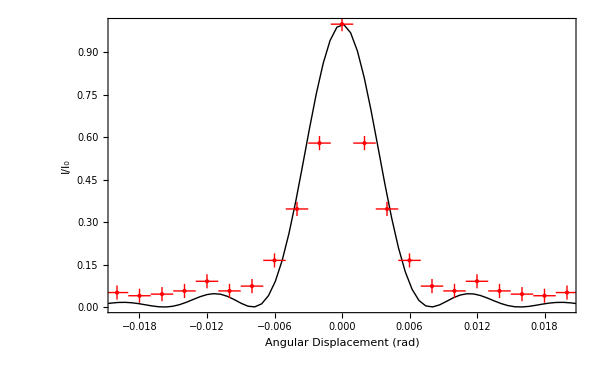

```mathematica
Show[{theory,dataPlot}]
```

TODO:  Figure out how to attaach the legend to the plot

```mathematica
Legend[{{Graphics[{Black,Line[{{0,0},{2,0}}]}],Style["   theory",Large]},{Graphics[{Red,Disk[{0,0.5},0.05],Line[{{0,0},{0,1}}],Line[{{-0.5,0.5},{0.5,0.5}}],Line[{{-0.05,1},{0.05,1}}],Line[{{-0.05,0},{0.05,0}}],Line[{{-0.5,0.46},{-0.5,0.54}}],Line[{{0.5,0.46},{0.5,0.54}}]}],Style["   data",Large]}}]//Graphics
```

-Graphics-